```mathematica
h[r_,th_]:=th/Abs[r]*Sin[Abs[r]/th]
dh[r_,th_]:=D[h[r,th],r]
ddh[r_,th_]:=D[dh[r,th],r]
```

```mathematica
dh[r,0.8]
```

(1. Cos[1.25 Abs[r]] Abs'[r])/Abs[r]-(0.8 Sin[1.25 Abs[r]] Abs'[r])/Abs[r]^2

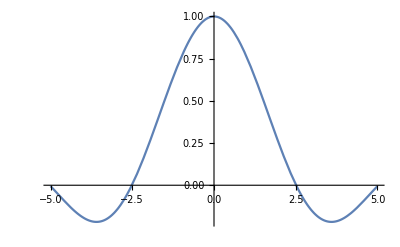

General::ivar: -4.9998 is not a valid variable.

General::ivar: -4.79571 is not a valid variable.

General::ivar: -4.59163 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

-Graphics-

General::ivar: -4.9998 is not a valid variable.

General::ivar: -4.79571 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[h[r,0.8],{r,-5,5}]
Plot[dh[r,0.8],{r,-5,5}]
Plot[ddh[r,0.8],{r,-5,5}]
```

```mathematica
Limit[Cos[Abs[r]]/r,r->0]
```

∞